```mathematica
Manipulate[Plot[func[myData[[i]],n,x],{x,0,2 π},PlotRange->{-2,2}],{i,1,5,1},{n,.5,1.5},Initialization:>(func[dat_,n_,x_]:=n Sin[dat*x];
myData={1,2,3,4,5})]
```

```mathematica
{Slider[Dynamic[x]],Dynamic[x]}
```

{,}

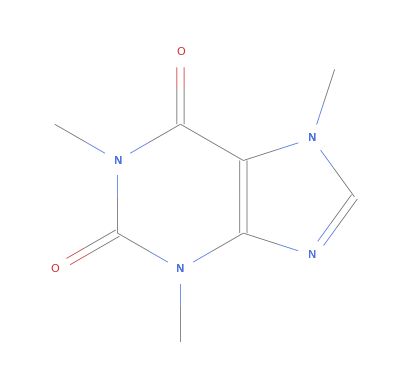

```mathematica
ChemicalData["Caffeine"]
```

```mathematica
ChemicalData["Caffeine","MoleculePlot"]
```

-Graphics3D-

```mathematica
ChemicalData["Caffeine","MolarMass"]
```

194.191

```mathematica
WordData["fish"]
```

{{fish,Noun,AquaticVertebrate},{fish,Noun,Food},{fish,Verb,Grab},{fish,Verb,Search}}

```mathematica
WordData["fish","PartsOfSpeech"]
```

{Noun,Verb}

```mathematica
WordData["fish","Definitions"]
```

{{fish,Noun,AquaticVertebrate}→any of various mostly cold-blooded aquatic vertebrates usually having scales and breathing through gills,{fish,Noun,Food}→the flesh of fish used as food,{fish,Verb,Grab}→catch or try to catch fish or shellfish,{fish,Verb,Search}→seek indirectly}

```mathematica
WordData["fish","Synonyms"]
```

{{fish,Noun,AquaticVertebrate}→{},{fish,Noun,Food}→{},{fish,Verb,Grab}→{},{fish,Verb,Search}→{angle}}

```mathematica
{Checkbox[False],Checkbox[True]}
```

{,}

```mathematica
{Checkbox[1,{1,2,3}],Checkbox[2,{1,2,3}],Checkbox[3,{1,2,3}]}
```

{,,}

```mathematica
PopupMenu[a,{a,b,c,d}]
```

```mathematica
{PopupMenu[Dynamic[x],{a,b,c,d}],Dynamic[x]}
```

{,}

```mathematica
{Slider[Dynamic[n],{0,100,1}],Dynamic[n]}
```

{,}

```mathematica
Manipulate[Graphics[Line[{{0,0},p}],PlotRange->2],{{p,{1,1}},Locator}]
```

```mathematica
g[x_]:=x
Manipulate[g[x],{x,0,1},SaveDefinitions->True,FrameLabel->"saved"]
```